# On Functional Iteration and Roots

## Introduction

## Abstract

This project explores non-integer iteration of functions of one or more variables. We present algebraic solutions to roots of some generalized functions, and detail various numerical and algebraic root-finding algorithms.

## Introduction

### Basic Definitions

Composition, denoted with the symbol ◦, involves inputting one function’s output into another’s input. For example, (f ◦ g)(x) is equivalent to f(g(x)). When the same function is composed with itself multiple times, it is said to be nested.

Let (f ◦ f ◦ f...)_n where n ∈ ℕ (i.e. nesting) be denoted f^n, where ◦ denotes composition. f^n may be  called the nth functional exponent of f.

#### Implementation

Helper function for overloading. For some reason, WL doesn’t treat all functions as having a head of Function. Don’t ask how it works.

```mathematica
FunctionQ[f_]:=Head[f]===Function||!((Information[f, "Definitions"][[0]]===Information)||Information[f, "Definitions"]===None)||(Quiet[Context[f],Context::ssle]==="System`"&&DownValues[f]==={})
```

Overloading Composition (i.e. @* operator) to do repeated composition

```mathematica
Unprotect[Composition];
Composition[f_?FunctionQ, n_Integer?Positive]:=Nest[f@*#&,f, n-1]
Composition[f_?FunctionQ, 0]:=#&
Protect[Composition];
```

Symbolic Example

```mathematica
f[x_]:=x^2
f@*4
```

f@*f@*f@*f

### Properties

Composition of the same nested function is additive, so f^n ◦ f^m = f^(n+m).
Nesting a nested function is multiplicative, so (f^n)^m=f^nm.
In these ways, functional exponentiation and composition have similar algebraic properties to algebraic exponentiation and multiplication, respectively.

### Generalized Nesting

#### Integers

Although nesting so far has only been defined for the natural numbers, it can be extended based on the properties above.
If we define f^0(x)=x and f^-n=(f^-1)^n (where f^-1 is the inverse function of f), then the above properties of composition and nesting now hold for integer nestings.

E.g. for some function f with an inverse f^-1:
By the definition of the inverse function, (f^1◦ f^-1)(x)=x
Equivalently, with our definitions and properties, (f^1◦ f^-1)(x)=f^(1-1)(x)=f^0(x)=x

#### Inverses and Rationals

In the same way that composition being additive leads to a generalization to the integers, nesting being multiplicative leads to a generalization to the rationals.
Let the mth functional root be denoted f^(1/m). This function has the property that nesting it m times will result in the original function f, because
(f^(1/m))^m=f^(m/m)=f^1

E.g. f^(1/2)◦ f^(1/2)=f^(1/2 + 1/2)=f^1
In other words, f’s square root g must satisfy g(g(x)) = f(x)

By the same logic, let the functional exponent f^(n/m) be defined as the mth root of f^n, or, equivalently, the nth nesting of the mth root of f.

#### Reals

For some w ∈ ℝ, define f^w(x) =lim_(i->∞) (f^(⌊2^i w⌋/⌊2^i⌋)(x)). This is simply the limit of a rational approximation of w.

#### Complexes

Occasionally, it may be even possible to generalize functional iteration to complex. That is, the ith exponent of f, f^𝕚, must satisfy the property that (f^𝕚)^𝕚=f^(𝕚^2)=f^-1.

#### Goal of the Project

In general, the goal of the project will be finding and exploring solutions or approximations of non-Integer functional exponents. Functions based on nesting, iteration, or exponentiation are called functional iterates.

## Explicit Solutions

Beyond trivial examples where f(f(x)) = f(x) (e.g. f(x) = a, f(x) = x, f(x) = Ramp(x)), here we will explore algebraic solutions to simple functional exponents.

### Helper Functions

Generates the coefficients of the powers of x. For example, f(x) =a_0+a_1 x+a_2 x^2... becomes {a_0, a_1...}.

```mathematica
coefList[symb_, {eMin_:0, eMax_:1}, var_:x, includeRemainder_:True]:=Module[{coefs},
coefs=Table[e->Plus@@(If[(#/.var->temp)===#, #,0]&/@(List@@Expand[symb var^-e])), {e, eMin, eMax}];
If[includeRemainder,Append[coefs, _->Expand[symb-(Values[coefs].(var^(Range[Length[coefs]]-1)))]],coefs]]

"Example:"
coefList[2+c+s x+s x^3+Log[x], {0, 3}, x]
```

Example:

{0→2+c,1→s,2→0,3→s,_→Log[x]}

## Affine Functions

An affine function is a function which can be written f(x) = a + b x. Using Solve[], one can find a simple, affine solution to the functional mth root of f.
This method only works if the structure of f^(1/2) is known. That is, the affine nature of f^(1/2) can be guessed, and because an exact solution exists, it can be seen that this guess is true. Such a structure becomes more difficult to find as a function becomes more complex, and is the main challenge in finding exact solutions to most functions.

```mathematica
m=7;
f[x_]:=a+b x
fRoot[x_]:=r+s x

  (* Find (f^(1/m))^m(x). Then, solve for the coefficients in f^(1/m) *)
fRootNested=(fRoot@*m)[x]//PowerExpand//Expand;

fCoefs=coefList[f[x], {0, 1}];  (* f is defined in terms of a and b *)
fRootCoefs=coefList[fRoot[x],{0, 1}];  (* f^(1/m) is defined in terms of r and s *)
fRootNestedCoefs=coefList[fRootNested,{0, 1}];  (* (f^(1/m))^m is defined in terms of various powers of r and s *)

fullSolution=Solve[
And@@Thread[#1==#2&[Values[fCoefs], Values[fRootNestedCoefs]]],  (* Set f(x) == (f^(1/m))^m(x) *)
Values[fRootCoefs[[;;-2]]]  (* Solve for the coefficients of f^(1/m) *)
];

(* Return the first solution (Most other solutions contain a root of a negative, so this is the only real-valued solution) *)
sol=Normal[Association[Join[{r->0, s->0},First[fullSolution]]]]
```

{r→(-a+a b^(1/7))/(-1+b),s→b^(1/7)}

Based on the above computation, a general mth root formula is given by:  f^(1/m)(x)=a(b^(1/m) -1)/(b-1)+b^(1/m)x
This can be extended to a general exponentiation formula for rationals,  reals, and complexes:  f^z(x)=a(b^z -1)/(b-1)+b^z x

```mathematica
Manipulate[
Labeled[
Plot[{a+b x, (a(b^z-1))/(b-1)+b^z x}, {x, -10, 10}, PlotRange->{-30, 30}],
"Plot of affine f and f^z"],
{z, -2, 2},
{a, -2, 2},
{b, 2^-16, 2}
]
```

```mathematica
Manipulate[
Labeled[
 Plot3D[(-a+a b^(1/m))/(-1+b)+b^(1/m)x, {x, -2, 2}, {m, -2, 2}],
"Plot of affine f and f^z over all z"]
,{a, -2, 2}, {b,2^-16, 2}]
```

## Power Functions / Monomials

One of the most useful ways of finding roots of functions is to first iterate them, then look for structure or formulas within the nested function which can be extended to noninteger nesting (i.e. root finding). Such a method was employed in order to find the general formula for functions of the form f(x)=a*x^b.

f^1(x)=a*x^b
f^2(x)=a*(a*x^b)^b=a^(1+b)*x^(b^2)
f^3(x)=a*(a*(a*x^b)^b)^b=a^(1+b+b^2)*x^(b^3)
f^4(x)=a*(a*(a*(a*x^b)^b)^b)^b=a^(1+b+b^2+b^3)*x^(b^4)

The pattern emerges that the nth nest of f is a^(b^0+b^1+...+b^(n-1))*x^(b^n)
Because that sum of powers of b is a geometric sequence, it can be replaced with the formula for a geometric sequence, and by this method the final formula is obtained:
f^n(x)=a^((b^n-1)/(b-1))x^(b^n)
Although this formula was defined in terms of discrete sums, by using the geometric sum formula, it may be generalized to all complex numbers:
f^z(x)=a^((b^z-1)/(b-1))x^(b^z)

```mathematica
j[a_,b_,x_, z_]:=a^((b^z-1)/(b-1))*x^(b^z)
Manipulate[
Labeled[
Plot[{1*x^2,j[1, 2, x, z]}, {x, 0, 1.2}, PlotRange->{-0.1, 1.54}],
"Plot of x^2 and it's zth exponent"],
 {z, -3, 3, 0.1}]
```

```mathematica
Manipulate[Labeled[Quiet[ComplexPlot[j[1, 2, xRe+I*xIm, z], {z, -10-10I, 10+10I}], General::munfl], "Plot of x^2 and it's zth exponent on the complex plane"], {xRe, -10, 10}, {xIm, -10, 10}]
```

## Inverse Function Composition

If one compares the formulas for the iterate of a monomial and the iterate of an affine function, many similarities may become apparent: the coefficients in one are closely related to the exponents of the other, and both share a similar structure. When given a monomial function M, if you compute ln(M(e^x)), you will see that it is an affine function. Let A(x)=ln(M(e^x)). If you find the zth functional exponent of both M and A, you will see that same relationship: A^z(x)=ln(f^z(e^x)).

Although easiest to identify in the case of affine and monomial, this can be generalized to all functions, and to all function-inverse function pairs:
If g(x)=j^-1(f(j(x))), then g^z(x)=j^-1(f^z(j(x))), provided j^-1 and j are defined over the required domains.

For a rational exponent z, this statement is fairly easy to prove. For example, if z=1/2:

Let g(x)=j^-1(f(j(x)))

g^(1/2)(g^(1/2)(x))=j^-1(f(j(x)))
g^(1/2)(g^(1/2)(x))=j^-1(f^(1/2)(f^(1/2)(j(x))))
g^(1/2)(g^(1/2)(x))=j^-1(f^(1/2)(j(j^-1(f^(1/2)(j(x))))))
g^(1/2)(x)=j^-1(f^(1/2)(j(x)))

And so we arrive at the above formula. As this method of proof can be generalized to all rational exponents, it can be extended to the reals and complexes through a similar method as given above for the extending of functional nesting into functional exponentiation.

## Formulas found by this technique

If  the exponent of a function f is known, by this technique, the exponent of any function of the form j^-1(f(j(x))) may be found (given some domain constraints on j^-1 and j.

### Cos(M(ArcCos(x)))

For example, because the formula for the iterate of a monomial M is known, one can find the iterate of a cos(M(arccos(x))):

M(x)=a*x^b
f(x)=cos(a*(arccos(x))^b)

M^z(x)=a^((b^z-1)/(b-1))x^(b^z)
f^z(x)=cos(a^((b^z-1)/(b-1))(arccos(x))^(b^z))

```mathematica
Manipulate[Labeled[Quiet[Plot[Cos[a^((b^(1/2)-1)/(b-1))ArcCos[x]^(b^(1/2))], {x, -1, 1}, PlotRange->{{-1,1}, {-1, 1}}], General::munfl], "Plot of f^(1/2)"], {a,3, 10}, {b, 3, 10}]
```

### ArcTan(M(Tan(x)))

ArcCos has a bounded range [-1, 1], so a different choice of j may lead to more interesting results. For example, arctan(M(tan(x))) for some monomial M:

M(x)=a*x^b
f(x)=arctan(a*(tan(x))^b)

M^z(x)=a^((b^z-1)/(b-1))x^(b^z)
f^z(x)=arctan(a^((b^z-1)/(b-1))(tan(x))^(b^z))

```mathematica
Manipulate[Labeled[Quiet[Plot[ArcTan[a^((b^z-1)/(b-1))Tan[x]^(b^z)], {x, -10, 10}, PlotRange->{All, {-Pi/2, Pi/2}}], General::munfl], "Plot of f^z"], {a,3, 10}, {b, 3, 10}, {z, -3, 3}]
```

### ln(sin(exp(x)))

Although an exact formula for sin^(1/2) is not known, an approximation can be found, which is what will be used here.

f(x)=ln(sin(exp(x)))

f^(1/2)(x)=ln(sin^(1/2)(exp(x)))

```mathematica
rootSinBasicApprox[theta_]:=Sin[theta]+Sin[Sin[theta]]-Sin[Sin[Sin[theta]]]
```

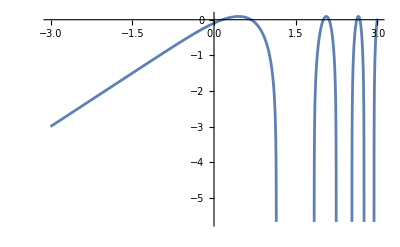
-Graphics-Plot of f^(1/2)

```mathematica
Labeled[Quiet[Plot[Log[rootSinBasicApprox[Exp[x]]], {x, -3, 3}], General::munfl], "Plot of f^(1/2)"]
```

And indeed, if this root is iterated with itself, it gives back the original function:

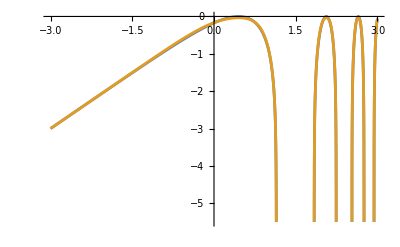
-Graphics-Plot of f and f^(1/2)◦f

```mathematica
Labeled[Quiet[Plot[{Log[Sin[Exp[x]]],Log[rootSinBasicApprox[Exp[Log[rootSinBasicApprox[Exp[x]]]]]]}, {x, -3, 3}], General::munfl], "Plot of f and f^(1/2)◦f"]
```

## Numerical Methods

As many functional roots are very difficult to find, and in many cases (such as polynomials on the full complex plane), are proven to have no solutions, this paper now examines methods for finding functional iterates (but mainly functional square roots) using numerical methods.

## Method 1: Recursive Function Values

#### Helper Functions

As many operations in this notebook take a very long time to run, this function gives an progress indicator for them:

```mathematica
progressMap[func_,l_List, message_:"Complete"]:=Module[{progress=PrintTemporary["0% "<>message]}, Table[NotebookDelete[progress];progress=PrintTemporary[ToString[Round[100*i/Length[l]]]<>"% "<>message]; func[l[[i]]],{i, Length[l]}]]
```

Makes a linear spline between points (i.e. connects them with straight lines), and extends the domain using the last two points on either end.

```mathematica
LinearSpline[points_][x_]:=Module[{p, m, xs,table},
p=Sort[points,#1[[1]]<#2[[1]]&];
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]
```

### Input

Input a function and a finite range over which the solution will be found. The step size indicates the distance between the points where error is calculated.

```mathematica
f[x_]:=Sin[x]+LogisticSigmoid[x];
originalRange={-2*Pi,2*Pi,0.3};
range=originalRange;
```

Here is a plot of the inputted function over the range:

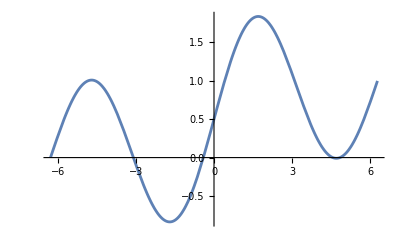

```mathematica
pRange=AbsoluteOptions[Plot[f[x], {x, range[[1]], range[[2]]}, ImageSize->Medium],PlotRange][[1,2]];
pRange[[2,1]]=Min[0,pRange[[2,1]]]; (* Set the plotting range manually *)

Plot[f[x],{x, range[[1]], range[[2]]}, PlotRange->pRange]
```

### Explanation

We are trying to solve the equation g(g(x)) = f(x) for all x.
Given an initial x, xi, we can make a guess as to the value of g:
g(xi) = w
Because we know that g(g(x)) = f(x), then g(g(xi)) = f(xi), and since g(xi) = w, then:
g(w) = f(xi)
This gives a second value of g. For a third, we can repeat the same thing. g(g(x)) = f(x), so g(g(w)) = f(w), and since g(w) = f(xi):
g(f(xi)) = f(w)
If you continue this, you get as many points as you want that will all lie on the g, assuming that g(xi) = w. By searching over all xi and all w, we can find the solution which minimizes the squared difference between a linear spline of the approximating points and the original function.

This is a function which more efficiently implements the process described above:

```mathematica
approximatingPoints[xii_,w_,n_:20]:=Riffle[Transpose[{NestList[f, xii, n], NestList[f, w, n]}],Transpose[{NestList[f, w, n], NestList[f, f[xii], n]}]]
```

FInally, here are more helper functions relating to it, which are fairly self-explanatory.

```mathematica
approxFunc[xii_, w_]:=LinearSpline[approximatingPoints[xii, w]]
error[af_]:=Quiet[Sum[(af[af[x]]-f[x])^2, {x, range[[1]], range[[2]], range[[3]]}]*range[[3]],General::munfl]
errorFunc[xii_, w_]:=error[approxFunc[xii,w]]
```

### Search

For every xii and w, the Search[] function checks the error of it, setting minP to be the values of xii and w which minimize error, and returning that minimum error. By then subdividing the region around minP, a better and better solution can be found. As the first iteration is the biggest search (in order to minimize the effect of local minima), it takes much longer than all other iterations.

```mathematica
(* Tweak the last value of each of these for faster first-step evaluation times. *)
xiiRange=range;wRange=range; 

search[anything___]:=(
points=ParallelTable[errorFunc[xii, w],{xii, xiiRange[[1]],  xiiRange[[2]],  xiiRange[[3]]}, {w, wRange[[1]],  wRange[[2]],  wRange[[3]]}];
minI=First[Position[points,Min[points],2]];
minP={xiiRange[[1]]+minI[[1]]xiiRange[[3]], wRange[[1]]+minI[[2]]wRange[[3]]};
minV=errorFunc@@minP;

xiiRange={minP[[1]]-xiiRange[[3]], minP[[1]]+xiiRange[[3]], 0.5xiiRange[[3]]};
wRange={minP[[2]]-wRange[[3]], minP[[2]]+ wRange[[3]], 0.5wRange[[3]]};

minV
);
```

```mathematica
PrintTemporary["The first step takes way longer than future steps"];
progressMap[search,Range[20]]
```

{145646.,553.154,15.6083,4.68805,3.48817,3.18523,3.07492,3.02761,3.00568,2.99513,2.98995,2.98739,2.98611,2.98547,2.98515,2.985,2.98492,2.98488,2.98486,2.98485}

### Output

Based on the search, here is the best function found so far:

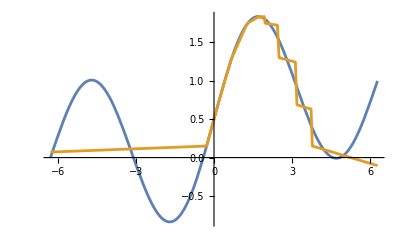

```mathematica
aFunc= approxFunc@@minP;
Plot[{f[x], aFunc[aFunc[x]]}, {x, range[[1]], range[[2]]}, PlotRange->pRange]
```

And here are the xii and w values, and the error which were achieved:

```mathematica
minP
minV
```

{4.21682,-0.283185}

2.98485

## Method 2: Simultaneous function value optimization

### Explanation

Instead of being smart about nesting functions with a single initial guess, this method tries to determine the whole function at once in order to move the values closer to what is needed. It is extremely susceptible to local minima, but it can often do a much better job of optimizing simpler functions, such as sine or some polynomials.

First, take a guess at a functional root g. I’ve used the g from method 1 here, but you could probably use almost anything. Next, find the differences between that and the original function:
delta(x) = f(x) - g(g(x))

Finally, simply add the delta vals to g:
new_g(x) = g(x) + temperature * delta(x)

For some points, g(x) will not be affected much, but g(g(x)) will be moved closer to f. In this case, g will be positively affected. For other points, it may shoot off to infinity or become discontinuous, so there is no real guarantee that this will work.

### Input

Input a function and a finite range over which the solution will be found. The step size indicates the distance between the points where error is calculated.

```mathematica
f[x_]:=Sin[x]+LogisticSigmoid[x];
originalRange={-2*Pi,2*Pi,0.3};
range=originalRange;
```

Here is a plot of the inputted function over the range:

```mathematica
pRange=AbsoluteOptions[Plot[f[x], {x, range[[1]], range[[2]]}, ImageSize->Medium],PlotRange][[1,2]];
pRange[[2,1]]=Min[0,pRange[[2,1]]]; (* Set the plotting range manually *)

Plot[f[x],{x, range[[1]], range[[2]]}, PlotRange->pRange]
```

-Graphics-

### Implementation

First, it represents both the original function and the approximation as a set of points, with xVals being the x values of the points, fVals being the corresponding y values of the original function, and aVals being the approximated y values.

```mathematica
range[[3]]=originalRange[[3]]/5;

aFunc= approxFunc@@minP;
xVals=Range@@range;
fVals=f/@xVals;
aVals=aFunc[aFunc[#]]&/@xVals;

(* Generates the interpolating function from a list of y values *)
funcFromVals[vals_]:=LinearSpline[Transpose[{xVals,  vals}]]
```

Here are plots of the interpolated values for the original function and the function from method 1:

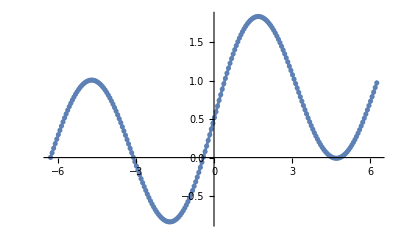

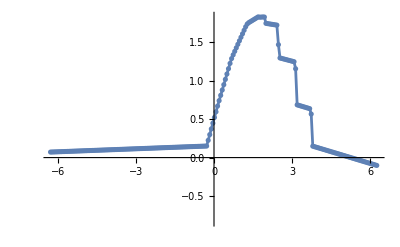

```mathematica
PlotVals[vals_]:=Show[{ListPlot[Transpose[{xVals, vals}], PlotRange->pRange], Plot[funcFromVals[vals][x], {x, range[[1]], range[[2]]}, PlotRange->pRange]}]
PlotVals[fVals]
PlotVals[aVals]
```

### Optimization

This repeatedly applies the method described to optimize the function.

```mathematica
aValsHist={aVals};
progressMap[
(aFunc=funcFromVals[aVals];
aVals=aVals+0.3*(fVals-ParallelMap[aFunc[aFunc[#]]&,xVals]);
AppendTo[aValsHist, aVals];)&,Range[50] , "Optimized"];

(* Find the optimization which actually minimized error *)
bestVals=aValsHist[[First[PositionSmallest[ParallelMap[error[funcFromVals[#]]&,aValsHist]]]]];
aFunc=funcFromVals[bestVals];
```

Plot the progress made so far:

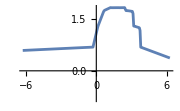
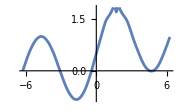
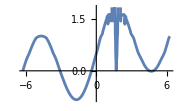
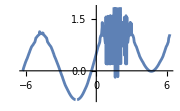
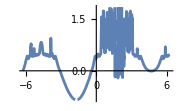

```mathematica
ParallelMap[With[{aFunc=funcFromVals[aValsHist[[#]]]},Plot[aFunc[aFunc[x]], {x, range[[1]], range[[2]]}, ImageSize->Small, PlotRange->pRange]]&, Round/@Subdivide[1, Length[aValsHist], 4]]
```

### Output

Plot the original and the best output:

-Graphics-

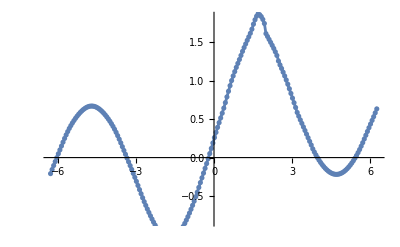

```mathematica
PlotVals[fVals]
PlotVals[bestVals]
```

## Method 3: Fourier Approximation and Analysis

For some functions like Sin and Cos, fourier series approximations of their roots converge very quickly, and so a good approximation can be found with relatively little computational power.

### Approximation of Sin(x)

For example, a 9th degree summation of sines can be minimized to a squared error of less than 10^-7:

```mathematica
n=9;  (* Number of Sine Terms *)
Clear[a];  (* Symboilic vector of coefficients *)

sol=Quiet[NMinimize[
Quiet[NIntegrate[
(Sin[x]-Sum[a[i]*Sin[i Sum[a[j]*Sin[j x],{j,n}]],{i,n}])^2,{x,-2Pi,2Pi}
]],
Table[a[i],{i,n}]
]];

approx[x_]:=Values[Last[sol]].Table[Sin[i x],{i,n}]
```

Error Value:

3.83823×10^-8

Sin Coefficients:

{a[1]→1.09381,a[2]→-6.69878×10^-8,a[3]→-0.038811,a[4]→1.18351×10^-7,a[5]→0.00582721,a[6]→-5.752×10^-8,a[7]→-0.00119246,a[8]→-4.52294×10^-7,a[9]→0.000241406}

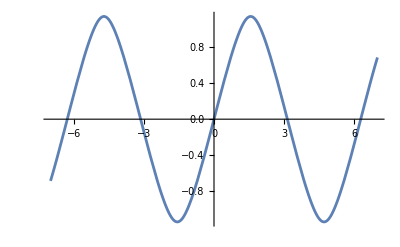
-Graphics-Taylor Series Sin^(1/2) Approximation

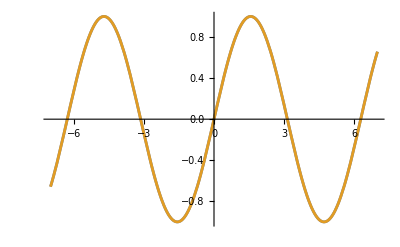
-Graphics-Sin and Sin^(1/2)(◦Sin)^(1/2)

```mathematica
"Error Value:"
sol[[1]]

"Sin Coefficients:"
sol[[2]]

Labeled[Plot[approx[x], {x, -7,7}], "Taylor Series Sin^(1/2) Approximation"]
Labeled[Plot[{Sin[x], approx[approx[x]]}, {x, -7,7}], "Sin and Sin^(1/2)(◦Sin)^(1/2)"]
```

If you plot the error value based on the first two terms of the fourier series, you get:

```mathematica
(* Iconized because of the amount of time it takes to compute *)
```

-Graphics3D-

### Approximation of Cos(2 Pi x)

Generally, the square root of Cos has been one of the hardest approximations to find. Almost every technique diverges or gives fairly useless approximations. However, fourier series based upon the sum of cosines is one of the only methods that is successful in this regard, as it is able to get a fairly decent approximation of Cos(2 Pi x):

```mathematica
poly[coef_][x_]:=Sum[coef[[i]] Cos[x * (i-1)], {i, Length[coef]}]
error[func_]:=NIntegrate[(Cos[2 Pi w]-func[w])^2, {w, -1,1}]
eFunc[coef_]:=error[poly[coef][poly[coef][#]]&]
```

```mathematica
n=6;  (* degree of the fourier series *)
sol=Quiet[NMinimize[eFunc[Table[z[i], {i, n}]], Table[z[i], {i, n}], Method->"NelderMead"]];
```

```mathematica
approx[x_]:=poly[Values[sol[[2]]]][x]
```

Error Value:

0.0144072

Cos Coefficients:

{z[1]→-17.0724,z[2]→14.6867,z[3]→21.3906,z[4]→-31.2455,z[5]→17.0824,z[6]→-3.88236}

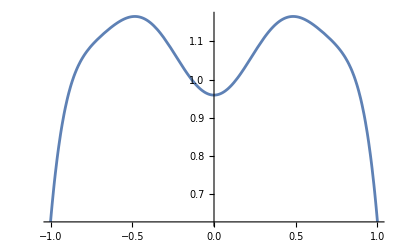
-Graphics-Taylor Series Cos^(1/2) Approximation

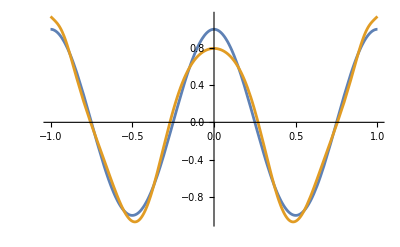
-Graphics-Cos and Cos^(1/2)(◦Cos)^(1/2)

```mathematica
"Error Value:"
sol[[1]]

"Cos Coefficients:"
sol[[2]]

Labeled[Plot[approx[x], {x, -1,1}], "Taylor Series Cos^(1/2) Approximation"]
Labeled[Plot[{Cos[2 * Pi * x], approx[approx[x]]}, {x, -1,1}], "Cos and Cos^(1/2)(◦Cos)^(1/2)"]
```

### Fourier Analysis

In addition to using fourier series to find new approximations of Sin and Cos, one may also use a fourier transform to analyze existing approximations, looking for patterns which may be used to find an exact formula. Although such an exact formula was not archived, it may be an area of future research to see if this approach is possible. Specifically, this section will investigate the fourier transform of sin^(1/2), because very close approximations have been found, while an exact formula has not.

#### Method 2 Sin Approximation

THIS SECTION IS JUST FOR COMPUTATION. It uses Method 2 to find an approximation of sin

Input a function and a finite range over which the solution will be found. The step size indicates the distance between the points where error is calculated.

```mathematica
f[x_]:=Sin[x];
originalRange={-2*Pi,2*Pi,0.3};
range=originalRange;
```

Here is a plot of the inputted function over the range:

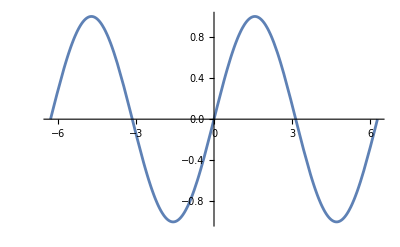

```mathematica
pRange=AbsoluteOptions[Plot[f[x], {x, range[[1]], range[[2]]}, ImageSize->Medium],PlotRange][[1,2]];
pRange[[2,1]]=Min[0,pRange[[2,1]]]; (* Set the plotting range manually *)

Plot[f[x],{x, range[[1]], range[[2]]}, PlotRange->pRange]
```

First, it represents both the original function and the approximation as a set of points, with xVals being the x values of the points, fVals being the corresponding y values of the original function, and aVals being the approximated y values.

```mathematica
range[[3]]=originalRange[[3]]/5;

aFunc= 0&;
xVals=Range@@range;
fVals=f/@xVals;
aVals=aFunc[aFunc[#]]&/@xVals;

(* Generates the interpolating function from a list of y values *)
funcFromVals[vals_]:=LinearSpline[Transpose[{xVals,  vals}]]
```

Here are plots of the interpolated values for the original function and the function from method 1:

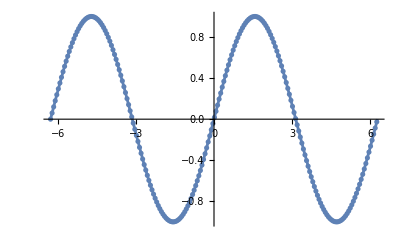

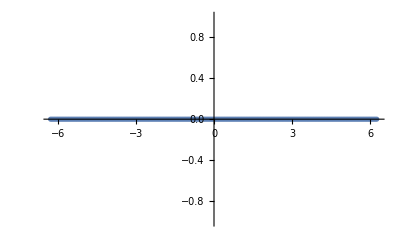

```mathematica
PlotVals[vals_]:=Show[{ListPlot[Transpose[{xVals, vals}], PlotRange->pRange], Plot[funcFromVals[vals][x], {x, range[[1]], range[[2]]}, PlotRange->pRange]}]
PlotVals[fVals]
PlotVals[aVals]
```

This repeatedly applies the method described to optimize the function.

```mathematica
aValsHist={aVals};
progressMap[
(aFunc=funcFromVals[aVals];
aVals=aVals+0.3*(fVals-ParallelMap[aFunc[aFunc[#]]&,xVals]);
AppendTo[aValsHist, aVals];)&,Range[50] , "Optimized"];

(* Find the optimization which actually minimized error *)
bestVals=aValsHist[[First[PositionSmallest[ParallelMap[error[funcFromVals[#]]&,aValsHist]]]]];
aFunc=funcFromVals[bestVals];
```

Plot the progress made so far:

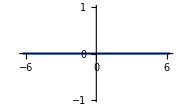
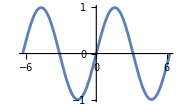
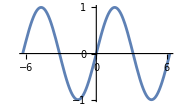
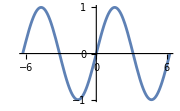
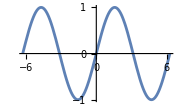

```mathematica
ParallelMap[With[{aFunc=funcFromVals[aValsHist[[#]]]},Plot[aFunc[aFunc[x]], {x, range[[1]], range[[2]]}, ImageSize->Small, PlotRange->pRange]]&, Round/@Subdivide[1, Length[aValsHist], 4]]
```

#### Fourier

```mathematica
p=Transpose[{xVals, Fourier[aVals]}];  (* Uses values from Method 2. Fourier transform of y values *)
pa={#1, Abs[#2]}&@@@p;  (* Absolute value of the points *)
p2=p[[15;;-15]];  (* Remove extreme values from p *)
pa2={#1, Abs[#2]}&@@@p2;
```

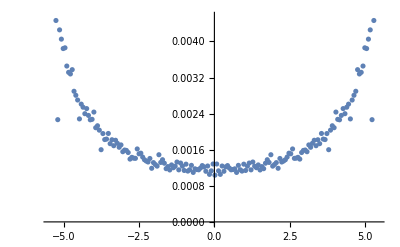
-Graphics-Plot of the Abs of the fourier terms of the approximation

```mathematica
Labeled[ListPlot[pa2], "Plot of the Abs of the fourier terms of the approximation"]
```

```mathematica
Labeled[ListPointPlot3D[{#1, Re[#2], Im[#2]}&@@@p2, AxesLabel->{"x", "Fourier Re", "Fourier Im"}, PlotRange->All], "Complex plot of the fourier terms of the approximation"]
```

-Graphics3D-Complex plot of the fourier terms of the approximation

While there definitely are some patterns to this data, and although many functions to approximate the data were tried, no exact solution was found.

## Method 4: Function and Nested Function Adjustment

This is an adaptation of method 2 which also uses some of the principles of nesting from method 1. It is an iterative approach, creating a new approximation each iteration from the previous.
let g_0

```mathematica
f[x_]:=Sin[x]
range={-2Pi, 2Pi, 0.3};
d=.05;
```

```mathematica
xVals=Range@@range;
g=AssociationThread[xVals, xVals];
```

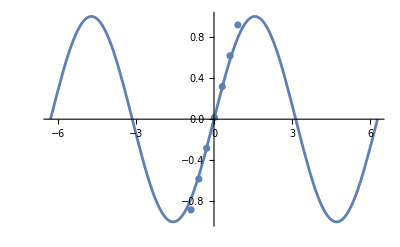

```mathematica
Show[Plot[f[x], {x, range[[1]], range[[2]]}], ListPlot[Transpose[{Keys[g], Values[g]}]]]
```

```mathematica
Der[f_, x_, dx_:10^-10]:=(f[x+dx]-f[x])/dx
(* Der[as_Association, val_]:=With[{a=KeySort[as]}, With[{i=First[First[Position[Keys[a],val]]]}, (Values[a][[i]]-Values[a][[i-1]])/(Keys[a][[i]]-Keys[a][[i-1]])]] *)
```

```mathematica
LinearSplineMod[points_][x_]:=Module[{p, m, xs,table},
p=points;
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]
```

```mathematica
AsLinSpl[as_Association,x_]:=LinearSpline[Transpose[{Keys[as], Values[as]}]][x]
AsLinSplMod[as_Association, x_]:=LinearSplineMod[Transpose[{Keys[as], Values[as]}]][x]
```

```mathematica
delta[x_]:=d*(f[x]-gf[gf[x]])
```

```mathematica
gf[x_]:=AsLinSplMod[g, x]
gnf[x_]:=AsLinSplMod[gn, x]
```

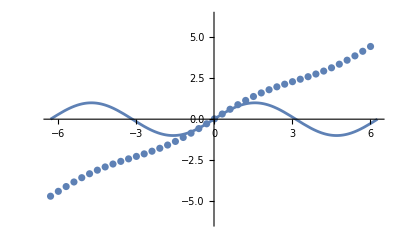

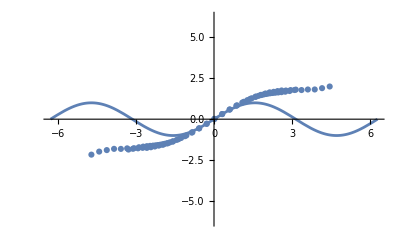

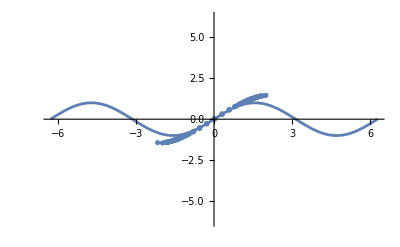

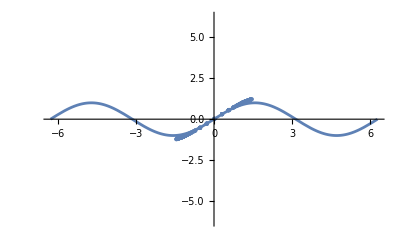

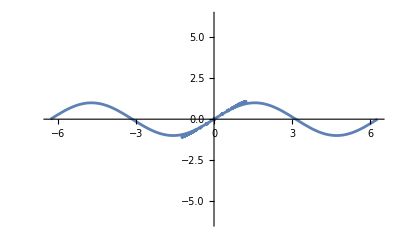

```mathematica
xVals=Range@@range;
g=AssociationThread[xVals, xVals];

plots={};
vals={};
Table[
gn=Association[];

d = 1/(i+1);

(gn[gf[#]]= gf[gf[#]]+0.8*delta[#])&/@Values[g];
(gn[#]= gf[#]+0.2*delta[#]/Der[gf, gf[#]])&/@Values[g];

AppendTo[vals,g=KeySort[gn]];

AppendTo[plots, Echo@Show[ListPlot[Transpose[{Keys[gn], Values[gn]}]], Plot[f[x], {x, range[[1]], range[[2]]}], PlotRange->{{range[[1]], range[[2]]}, {range[[1]], range[[2]]}}]]
, {i, 5}];
```